```mathematica
numIter = 10;
xn = 4.0;
f[x_]=x^3-3x-8.125;
fp[x_]=D[f[x],x];
For[i=1, i<= numIter, i++,
xnp1 = xn - (f[xn]/fp[xn]);
Print["xn= ", xn, " xnp1= ",xnp1];
xn=xnp1;

];
```

xn= 4. xnp1= 3.025

xn= 3.025 xnp1= 2.59638

xn= 2.59638 xnp1= 2.50415

xn= 2.50415 xnp1= 2.50001

xn= 2.50001 xnp1= 2.5

xn= 2.5 xnp1= 2.5

xn= 2.5 xnp1= 2.5

xn= 2.5 xnp1= 2.5

«2 more identical outputs»

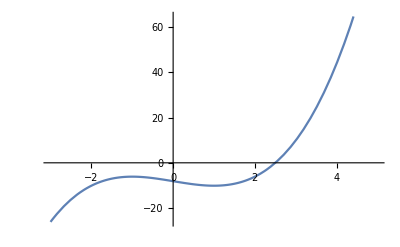

```mathematica
Plot[f[x],{x,-3,5}]
```